Problem Set 3

A
A1:
a)

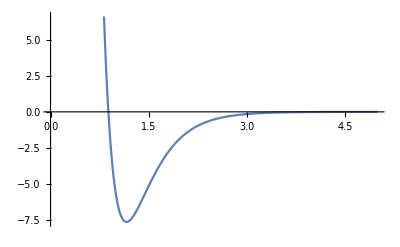

```mathematica
VMorse[r_]:=depth*(Exp[-2*α*(r-dis)]-2*Exp[-α*(r-dis)]);
VAB[r_] = VMorse[r];
VBC[r_] = VMorse[r];
subsAB = {depth-> 7.65, α-> 2.5, dis-> 1.162};
subsBC = {depth-> 7.65, α-> 2.5, dis -> 1.162};
Plot[VAB[r]/.subsAB,{r,0,5}]
```

b)

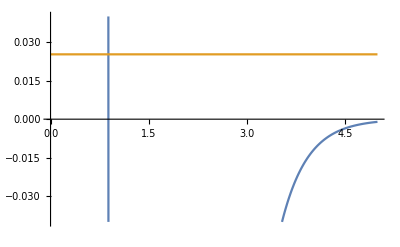

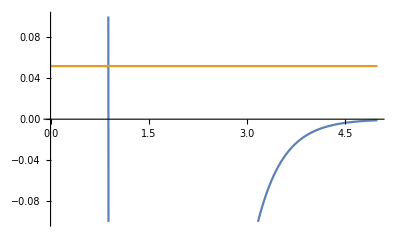

```mathematica
kb = 8.617*10^(-5);
Et[T_]:= kb*T;
Plot[{VAB[r]/.subsAB,Et[293]},{r,0,5},PlotRange->{-0.04,0.04}]
Plot[{VAB[r]/.subsAB,Et[600]},{r,0,5},PlotRange->{-0.1,0.1}]
```

c)

-Graphics3D-

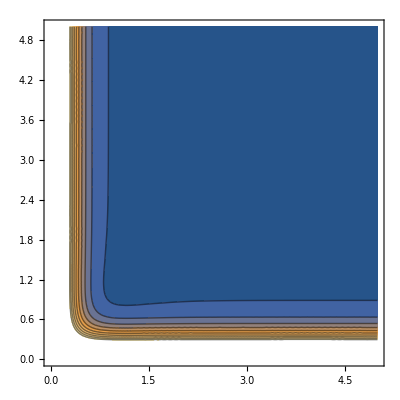

```mathematica
V2D[rAB_,rBC_] := (VAB[rAB]/.subsAB )+ (VBC[rBC]/.subsBC);
bAB = 1.162;
bBC = 1.162;
Plot3D[V2D[rAB,rBC],{rAB,0,5},{rBC,0,5}]
ContourPlot[V2D[rAB,rBC],{rAB,0,5},{rBC,0,5}]
```

```mathematica
V2D[bAB,bBC]
```

-15.3

Yes, this is consistent, this is the value of the sum of the potential well depths for each potential, i.e d_BC + d_AB

The plots above represent the condition when the CO bonds are at their optimal distance, which is the equilibrium distance of 1.162 Angstrom.

d)

```mathematica
Clear[xAA,xBB,xCC,vAA,vBB,vCC,divABB,divBCC,faa,fbb,fcc]
V2D[rAB_,rBC_] := (VAB[rAB]/.subsAB )+ (VBC[rBC]/.subsBC);

maa=16;
mbb=12;
mcc=16;
bAB = 1.162;
bBC = 1.162;
xAA[0] = -bAB -0.18;
xBB[0] = -0.28;
xCC[0] = bBC + 0.21;
vAA[0] = 0;
vBB[0] = 0;
vCC[0] = 0;
divABB[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCC[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faa[0] = divABB[xBB[0] - xAA[0],xCC[0]-xBB[0]];
fbb[0] = -divABB[xBB[0] - xAA[0],xCC[0]-xBB[0]] + divABB[xBB[0]-xAA[0],xCC[0]-xBB[0]];
fcc[0] = -divBCC[xBB[0]-xAA[0],xCC[0]-xBB[0]];
```

```mathematica
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAA[n+1] = xAA[n] + dt*vAA[n] + 1/2*faa[n]/maa *dt^2;
xBB[n+1] = xBB[n] + dt*vBB[n]+1/2 *fbb[n]/mbb *dt^2;
xCC[n+1] = xCC[n] + dt*vCC[n]+1/2 *fcc[n]/mcc*dt^2;
faa[n + 1] = divABB[xBB[n + 1] - xAA[n + 1],xCC[n + 1]-xBB[n + 1]];
fbb[n + 1] = -divABB[xBB[n + 1 ] - xAA[n + 1],xCC[n + 1]-xBB[n + 1]] + divABB[xBB[n + 1]-xAA[n+1],xCC[n + 1]-xBB[n + 1]];
fcc[n + 1] = -divBCC[xBB[n + 1]-xAA[0],xCC[n + 1]-xBB[n + 1]];
vAA[n+1] = vAA[n] + dt/(2*maa)*(faa[n] + faa[n+1]);
vBB[n+1] = vBB[n] + dt/(2*mbb)*(fbb[n] + fbb[n+1]);
vCC[n+1] = vCC[n] + dt/(2*mcc)*(fcc[n] + fcc[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBB[n]-xAA[n],xCC[n]-xBB[n]},{n,0,nSteps}]; 
Vrdata = Table[vAA[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAA[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAA[n],0},{xBB[n],0},{xCC[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

e)

```mathematica
xAAe[0] = -bAB -0.35;
xBBe[0] = -0.30;
xCCe[0] = bBC + 0.35;
vAAe[0] = 0;
vBBe[0] = 0;
vCCe[0] = 0;
divABBe[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCe[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faae[0] = divABBe[xBBe[0] - xAAe[0],xCCe[0]-xBBe[0]];
fbbe[0] = -divABBe[xBBe[0] - xAAe[0],xCCe[0]-xBBe[0]] + divABBe[xBBe[0]-xAAe[0],xCCe[0]-xBBe[0]];
fcce[0] = -divBCCe[xBBe[0]-xAAe[0],xCCe[0]-xBBe[0]];
```

```mathematica
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAe[n+1] = xAAe[n] + dt*vAAe[n] + 1/2*faae[n]/maa *dt^2;
xBBe[n+1] = xBBe[n] + dt*vBBe[n]+1/2 *fbbe[n]/mbb *dt^2;
xCCe[n+1] = xCCe[n] + dt*vCCe[n]+1/2 *fcce[n]/mcc*dt^2;
faae[n + 1] = divABBe[xBBe[n + 1] - xAAe[n + 1],xCCe[n + 1]-xBBe[n + 1]];
fbbe[n + 1] = -divABBe[xBBe[n + 1 ] - xAAe[n + 1],xCCe[n + 1]-xBBe[n + 1]] + divABBe[xBBe[n + 1]-xAAe[n+1],xCCe[n + 1]-xBBe[n + 1]];
fcce[n + 1] = -divBCCe[xBBe[n + 1]-xAAe[0],xCCe[n + 1]-xBBe[n + 1]];
vAAe[n+1] = vAAe[n] + dt/(2*maa)*(faae[n] + faae[n+1]);
vBBe[n+1] = vBBe[n] + dt/(2*mbb)*(fbbe[n] + fbbe[n+1]);
vCCe[n+1] = vCCe[n] + dt/(2*mcc)*(fcce[n] + fcce[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBBe[n]-xAAe[n],xCCe[n]-xBBe[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAe[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAe[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAAe[n],0},{xBBe[n],0},{xCCe[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

f)

```mathematica
xAAf[0] = -bAB -0.05;
xBBf[0] = -0.10;
xCCf[0] = bBC + 0.05;
vAAf[0] = 0;
vBBf[0] = 0;
vCCf[0] = 0;
divABBf[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCf[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaf[0] = divABBf[xBBf[0] - xAAf[0],xCCf[0]-xBBf[0]];
fbbf[0] = -divABBf[xBBf[0] - xAAf[0],xCCf[0]-xBBf[0]] + divABBf[xBBf[0]-xAAf[0],xCCf[0]-xBBf[0]];
fccf[0] = -divBCCf[xBBf[0]-xAAf[0],xCCf[0]-xBBf[0]];
```

```mathematica
time = 30.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAf[n+1] = xAAf[n] + dt*vAAf[n] + 1/2*faaf[n]/maa *dt^2;
xBBf[n+1] = xBBf[n] + dt*vBBf[n]+1/2 *fbbf[n]/mbb *dt^2;
xCCf[n+1] = xCCf[n] + dt*vCCf[n]+1/2 *fccf[n]/mcc*dt^2;
faaf[n + 1] = divABBf[xBBf[n + 1] - xAAf[n + 1],xCCf[n + 1]-xBBf[n + 1]];
fbbf[n + 1] = -divABBf[xBBf[n + 1 ] - xAAf[n + 1],xCCf[n + 1]-xBBf[n + 1]] + divABBf[xBBf[n + 1]-xAAf[n+1],xCCf[n + 1]-xBBf[n + 1]];
fccf[n + 1] = -divBCCf[xBBf[n + 1]-xAAf[0],xCCf[n + 1]-xBBf[n + 1]];
vAAf[n+1] = vAAf[n] + dt/(2*maa)*(faaf[n] + faaf[n+1]);
vBBf[n+1] = vBBf[n] + dt/(2*mbb)*(fbbf[n] + fbbf[n+1]);
vCCf[n+1] = vCCf[n] + dt/(2*mcc)*(fccf[n] + fccf[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBBf[n]-xAAf[n],xCCf[n]-xBBf[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAf[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAf[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAAf[n],0},{xBBf[n],0},{xCCf[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

A2: Frequency of oscillations
a)

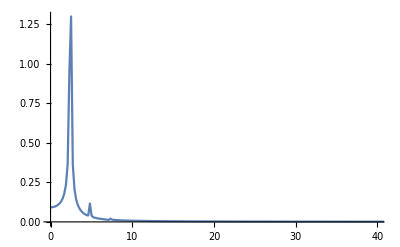

```mathematica
frData=Abs[Fourier[Vrdata]];
fData=Table[{2 Pi/time(n-1),frData[[n]]},{n,1,nSteps}];
ListPlot[fData,PlotRange->{{0,40},All}, Joined->True]
```

b) The resolution for the plot above is calculated by finding the distance between two peaks positions and dividing them by the combine widths. The resolution from the first two peaks is approximately 2.11 and the resolution from peak 2 to 3 is approximately  2.03, the width of the third peak is so small that it was ignored in the resolution calculations.

c) The largest frequency obtained is approximately 2.21, which is the x-coordinate in the plot above.

d) The frequencies in inverse seconds is calculated by taking the x-coordinate in the plot above and dividing it by 2Pi. The angular frequencies for the first peak is 2.21/2Pi = 3.47 and the second peak is 4.68/2PI = 7.35.

e)

```mathematica
maaa=16;
mbbb=12;
mccc=16;
xAAff[0] = -bAB -0.05;
xBBff[0] = -0.10;
xCCff[0] = bBC + 0.05;
vAAff[0] = 0;
vBBff[0] = 0;
vCCff[0] = 0;
divABBff[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCff[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaff[0] = divABBff[xBBff[0] - xAAff[0],xCCff[0]-xBBff[0]];
fbbff[0] = -divABBff[xBBff[0] - xAAff[0],xCCff[0]-xBBff[0]] + divABBff[xBBff[0]-xAAff[0],xCCff[0]-xBBff[0]];
fccff[0] = -divBCCff[xBBff[0]-xAAff[0],xCCff[0]-xBBff[0]];
```

```mathematica
time = 15.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAff[n+1] = xAAff[n] + dt*vAAff[n] + 1/2*faaff[n]/maaa *dt^2;
xBBff[n+1] = xBBff[n] + dt*vBBff[n]+1/2 *fbbff[n]/mbbb *dt^2;
xCCff[n+1] = xCCff[n] + dt*vCCff[n]+1/2 *fccff[n]/mccc*dt^2;
faaff[n + 1] = divABBff[xBBff[n + 1] - xAAff[n + 1],xCCff[n + 1]-xBBff[n + 1]];
fbbff[n + 1] = -divABBff[xBBff[n + 1 ] - xAAff[n + 1],xCCff[n + 1]-xBBff[n + 1]] + divABBff[xBBff[n + 1]-xAAff[n+1],xCCff[n + 1]-xBBff[n + 1]];
fccff[n + 1] = -divBCCff[xBBff[n + 1]-xAAff[0],xCCff[n + 1]-xBBff[n + 1]];
vAAff[n+1] = vAAff[n] + dt/(2*maaa)*(faaff[n] + faaff[n+1]);
vBBff[n+1] = vBBff[n] + dt/(2*mbbb)*(fbbff[n] + fbbff[n+1]);
vCCff[n+1] = vCCff[n] + dt/(2*mccc)*(fccff[n] + fccff[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBBff[n]-xAAff[n],xCCff[n]-xBBff[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAff[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAff[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAAff[n],0},{xBBff[n],0},{xCCff[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

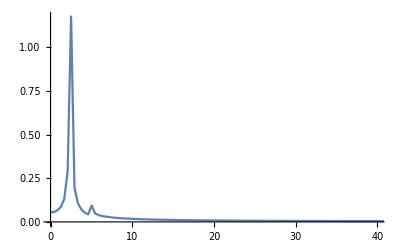

```mathematica
frData=Abs[Fourier[Vrdata]];
fData=Table[{2 Pi/time(n-1),frData[[n]]},{n,1,nSteps}];
ListPlot[fData,PlotRange->{{0,40},All}, Joined->True]
```

Changing the length of the time interval results in a lost of the third peak and compared to the first simulation the resolution of this fourier transform is worst.

f)

```mathematica
maaas=16;
mbbbs=12;
mcccs=16;
xAAffs[0] = -bAB -0.02;
xBBffs[0] = -0.10;
xCCffs[0] = bBC + 0.02;
vAAffs[0] = 0;
vBBffs[0] = 0;
vCCffs[0] = 0;
divABBffs[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCffs[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaffs[0] = divABBffs[xBBffs[0] - xAAffs[0],xCCffs[0]-xBBffs[0]];
fbbffs[0] = -divABBffs[xBBffs[0] - xAAffs[0],xCCffs[0]-xBBffs[0]] + divABBffs[xBBffs[0]-xAAffs[0],xCCffs[0]-xBBffs[0]];
fccffs[0] = -divBCCffs[xBBffs[0]-xAAffs[0],xCCffs[0]-xBBffs[0]];
```

```mathematica
time = 15.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAffs[n+1] = xAAffs[n] + dt*vAAffs[n] + 1/2*faaffs[n]/maaas *dt^2;
xBBffs[n+1] = xBBffs[n] + dt*vBBffs[n]+1/2 *fbbffs[n]/mbbbs *dt^2;
xCCffs[n+1] = xCCffs[n] + dt*vCCffs[n]+1/2 *fccffs[n]/mcccs*dt^2;
faaffs[n + 1] = divABBffs[xBBffs[n + 1] - xAAffs[n + 1],xCCffs[n + 1]-xBBffs[n + 1]];
fbbffs[n + 1] = -divABBffs[xBBffs[n + 1 ] - xAAffs[n + 1],xCCffs[n + 1]-xBBffs[n + 1]] + divABBffs[xBBffs[n + 1]-xAAffs[n+1],xCCffs[n + 1]-xBBffs[n + 1]];
fccffs[n + 1] = -divBCCffs[xBBffs[n + 1]-xAAffs[0],xCCffs[n + 1]-xBBffs[n + 1]];
vAAffs[n+1] = vAAffs[n] + dt/(2*maaas)*(faaffs[n] + faaffs[n+1]);
vBBffs[n+1] = vBBffs[n] + dt/(2*mbbbs)*(fbbffs[n] + fbbffs[n+1]);
vCCffs[n+1] = vCCffs[n] + dt/(2*mcccs)*(fccffs[n] + fccffs[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBBffs[n]-xAAffs[n],xCCffs[n]-xBBffs[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAffs[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAffs[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAAffs[n],0},{xBBffs[n],0},{xCCffs[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```

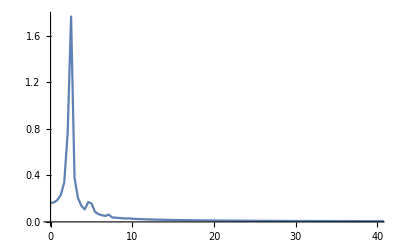

```mathematica
frData=Abs[Fourier[Vrdata]];
fData=Table[{2 Pi/time(n-1),frData[[n]]},{n,1,nSteps}];
ListPlot[fData,PlotRange->{{0,40},All}, Joined->True]
```

g) 
the frequency of the main peak is the x-coordinate were the peak is at a maximum, which about 2.2.The second peak frequency is about 4.69 and the third peak is around 7.04.

h)

```mathematica
maaass=2;
mbbbss=12;
mcccss=2;
xAAffss[0] = -1.162;
xBBffss[0] = -0.10;
xCCffss[0] = 0;
vAAffss[0] = 0;
vBBffss[0] = 0;
vCCffss[0] = 0;
divABBffss[rAB_,rBC_]=D[V2D[rAB,rBC],rAB];
divBCCffss[rAB_,rBC_] = D[V2D[rAB,rBC],rBC];
faaffss[0] = divABBffss[xBBffss[0] - xAAffss[0],xCCffss[0]-xBBffss[0]];
fbbffss[0] = -divABBffss[xBBffss[0] - xAAffss[0],xCCffss[0]-xBBffss[0]] + divABBffss[xBBffss[0]-xAAffss[0],xCCffss[0]-xBBffss[0]];
fccffss[0] = -divBCCffss[xBBffss[0]-xAAffss[0],xCCffss[0]-xBBffss[0]];
```

```mathematica
time = 15.0;
dt = 0.04;
nSteps = Round[time/dt];
Do[
xAAffss[n+1] = xAAffss[n] + dt*vAAffss[n] + 1/2*faaffss[n]/maaass *dt^2;
xBBffss[n+1] = xBBffss[n] + dt*vBBffss[n]+1/2 *fbbffss[n]/mbbbss *dt^2;
xCCffss[n+1] = xCCffss[n] + dt*vCCffss[n]+1/2 *fccffss[n]/mcccss*dt^2;
faaffss[n + 1] = divABBffss[xBBffss[n + 1] - xAAffss[n + 1],xCCffss[n + 1]-xBBffss[n + 1]];
fbbffss[n + 1] = -divABBffss[xBBffss[n + 1 ] - xAAffss[n + 1],xCCffss[n + 1]-xBBffss[n + 1]] + divABBffss[xBBffss[n + 1]-xAAffss[n+1],xCCffss[n + 1]-xBBffss[n + 1]];
fccffss[n + 1] = -divBCCffss[xBBffss[n + 1]-xAAffss[0],xCCffss[n + 1]-xBBffss[n + 1]];
vAAffss[n+1] = vAAffss[n] + dt/(2*maaass)*(faaffss[n] + faaffss[n+1]);
vBBffss[n+1] = vBBffss[n] + dt/(2*mbbbss)*(fbbffss[n] + fbbffss[n+1]);
vCCffss[n+1] = vCCffss[n] + dt/(2*mcccss)*(fccffss[n] + fccffss[n+1]),
{n,0,nSteps}]
```

```mathematica
rData = Table[{xBBffs[n]-xAAffs[n],xCCffs[n]-xBBffs[n]},{n,0,nSteps}]; 
Vrdata = Table[vAAffs[n],{n,0,nSteps}];
Vdata = Table[{n dt ,vAAffs[n]},{n,0,nSteps}];
Animate[ListPlot[{{xAAffs[n],0},{xBBffs[n],0},{xCCffs[n],0}},PlotStyle->PointSize[0.5],PlotRange->{{-3.0,3.0},{-1,1}}],{n,0,nSteps,1}]
```